Evaluate the evaluation cells of the other important notebooks

```mathematica
NotebookEvaluate[NotebookDirectory[]<>"directMat-2.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"periods.nb",EvaluationElements->Automatic];
NotebookEvaluate[NotebookDirectory[]<>"WeylTest.nb",EvaluationElements->Automatic];
```

Given some function f_L[k,l] generate the corresponding matrix

```mathematica
DirectFMat[L_,f_]:=Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=f[L,k,l];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

```mathematica
DirectFMatN[L_,f_,NPrec_]:=
Module[{k,n,l,tempMat},
tempMat=ConstantArray[0,{L,L}];
Do[tempMat[[k,l]]=N[f[L,k,l],NPrec];
,{k,1,L},{l,1,L}];
Return[tempMat,Module];
]
```

Similar to directMat.nb for the A matrix, generate the LxL precursor matrix for the C matrix

```mathematica
DirectCMat[L_]:=DirectFMat[L,(1/#1^2 Exp[I*2*Pi*(#2-#3)/#1])&]
```

```mathematica
DirectCMatN[L_,NPrec_]:=DirectFMatN[L,(1/#1^2 Exp[I*2*Pi*(#2-#3)/#1])&,NPrec]
```

Can use the exact same algorithm for tracing over half the d.o.f. as in directMat.nb

```mathematica
DirectTracedCMat[L_,l1_,l2_]:=
DirectTracedMat[L,l1,l2,DirectCMat[L]]
```

```mathematica
DirectTracedCMatN[L_,l1_,l2_,NPrec_]:=
DirectTracedMat[L,l1,l2,DirectCMatN[L,NPrec]]
```

Can also use the same algorithm for getting the reduced matrix by applying the zero mode constraint

```mathematica
DirectRedTracedCMat[L_,l1_,l2_]:=DirectRedTracedMat[L,l1,l2,DirectCMat[L]]
```

```mathematica
DirectRedTracedCMatN[L_,l1_,l2_,NPrec_]:=DirectRedTracedMat[L,l1,l2,DirectCMatN[L,NPrec]]
```

### Checking relation of reduced and non reduced matrices:

adjust the values here and then evaluate the whole subsection

```mathematica
L=32;
l1=7;
l2=4;
prec=15;
```

```mathematica
A1=DirectTracedMatN[L,l1,l2,prec]//Chop; (*A matrix*)
```

```mathematica
redA1=DirectRedTracedMatN[L,l1,l2,prec]//Chop; (*reduced A matrix *)
```

```mathematica
S1=Eigenvectors[A1]//Chop; (*matrix which diagonalizes A, its last row corresponds to the zero mode, which is given by \sum_{k=1}^{L/2} X(k)*)
S1[[-1]] (*display the last row, every element should be equal*)
```

{-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25,-0.25}

```mathematica
invS1=Transpose[S1]//Chop;
```

```mathematica
D1=Transpose[invS1].A1.invS1//Chop; (*diagonalized version of A, its last (bottom right) eigenvalue is zero*)
```

```mathematica
redD1=D1[[;;-2,;;-2]]; (*(L/2-1) x (L/2-1) version of the diagonal matrix, with the last row and column removed*)
```

```mathematica
C1=DirectTracedCMatN[L,l1,l2,prec]//Chop; (*C matrix*)
```

```mathematica
redC1=DirectRedTracedCMatN[L,l1,l2,prec]//Chop; (*reduced C matrix*)
```

```mathematica
M1=Transpose[invS1].C1.invS1//Chop; (*C matrix transformed into the diagonal basis of A*)
```

```mathematica
(*confirming that the last row and column of M are zero, i.e. no dependence on the zero mode*)
M1[[;;,-1]]
M1[[-1;;]]
```

{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

{{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}}

```mathematica
redM1=M1[[;;-2,;;-2]]; (*(L/2-1) x (L/2-1) version of the M matrix, with the last row and column removed*)
```

```mathematica
Tr[redM1.Inverse[redD1]] 
Tr[redC1.Inverse[redA1]]//Chop (*compare with the above*)
```

0.006732596995891

0.006732596995891

```mathematica
Clear[L,l1,l2,prec,A1,redA1,S1,invS1,D1,redD1,C1,redC1,M1,redM1];
prec=100;
```

### Calculating tr(CA^-1):

For a given L, l1, l2 this will find \wt{C}, \wt{A}, and f. Then print tr(\wt{C} \wt{A}^{-1}), then print the periods, normalized so that the period of the a cycle is 1. It finally outputs 
{τ2, tr( \wt{C} \wt{A}^{-1}) / | \hat{f}(0)|^2}

```mathematica
findTrCA[L_,l1_,l2_,AMat_,CMat_]:=Module[{l3,redA,invA,redC,tr,f,per,perRed},
l3=L/2-l1-l2;
redA=DirectRedTracedMat[L,l1,l2,AMat];
(*Print[1];*)
redC=DirectRedTracedMat[L,l1,l2,CMat];
(*Print[2];*)
invA=Inverse[redA];
(*Print[3];*)
f=CylEqnFastOptimized[l1,l2,l3,z];
(*Print[4];*)
Print[tr=Tr[redC . invA]];
per=PeriodsFastGivenF[l1,l2,l3,l1/2,l2/2,l3/2,f,z];
Print[perRed=per/per[[1]]];
(*Print[1/(1-perRed[[2]])];*)

(*Note that 1/per[[1]] is \hat{f}(0)*)
Return[{Im[perRed[[2]]],Re[tr*Abs[per[[1]]]^2]},Module]
]
```

```mathematica
(*if no precursor matrices provided, generate them first*)
findTrCA[L_,l1_,l2_]:=findTrCA[L,l1,l2,DirectMatN[L,prec],DirectCMatN[L,prec]]
```

Running tests to see if tr(\wt{C} \wt{A}^{-1}) \propto |\hat{f}(0)|^2/ τ2

```mathematica
setL=310;
prec=15;
(*Since we want to test different τ at the same L, useful to store the precursor matrices*)
AMat=DirectMatN[setL,prec];
CMat=DirectCMatN[setL,prec];
```

```mathematica
(*make sure l1,l2,l3 are odd. Here we use l1=l2=k, l3=L/2-2k so it's important that L/2 and k are odd*)
L1=Table[
Print[k];
findTrCA[setL,k,k,AMat,CMat]
,{k,1,77,2}]
```

1

0.1018635688656+0. ⅈ

{1.+0. ⅈ,0.96148+0.274875 ⅈ,-0.0406205+0.289864 ⅈ}

3

0.08557485569812+0. ⅈ

{1.+1.38778×10^-17 ⅈ,0.934524+0.355899 ⅈ,-0.0652778+0.354824 ⅈ}

5

0.07545780579988+0. ⅈ

{1.+0. ⅈ,0.916834+0.399269 ⅈ,-0.0832213+0.399534 ⅈ}

7

0.06741244951662+0. ⅈ

{1.-1.38778×10^-17 ⅈ,0.900453+0.434952 ⅈ,-0.0995235+0.434852 ⅈ}

9

0.06051690181521+0. ⅈ

{1.+0. ⅈ,0.885045+0.465505 ⅈ,-0.114967+0.465553 ⅈ}

11

0.05439788645377+0. ⅈ

{1.+0. ⅈ,0.869982+0.493084 ⅈ,-0.130011+0.493058 ⅈ}

13

0.04886568687005+0. ⅈ

{1.+0. ⅈ,0.855128+0.518417 ⅈ,-0.144877+0.518433 ⅈ}

15

0.04381100575745+0. ⅈ

{1.+0. ⅈ,0.840281+0.542151 ⅈ,-0.159716+0.54214 ⅈ}

17

0.03916566152921+0. ⅈ

{1.+0. ⅈ,0.825372+0.56459 ⅈ,-0.174631+0.564597 ⅈ}

19

0.03488471175527+0. ⅈ

{1.+1.38778×10^-17 ⅈ,0.810299+0.586017 ⅈ,-0.1897+0.586012 ⅈ}

21

0.03093728946557+0. ⅈ

{1.-1.38778×10^-17 ⅈ,0.795015+0.60659 ⅈ,-0.204987+0.606594 ⅈ}

23

0.0273014776544+0. ⅈ

{1.+0. ⅈ,0.779455+0.626458 ⅈ,-0.220544+0.626455 ⅈ}

25

0.02396124390897+0. ⅈ

{1.+0. ⅈ,0.76358+0.645713 ⅈ,-0.236421+0.645715 ⅈ}

27

0.02090450652791+0. ⅈ

{1.-2.77556×10^-17 ⅈ,0.747341+0.664441 ⅈ,-0.252659+0.664439 ⅈ}

29

0.01812185964157+0. ⅈ

{1.+0. ⅈ,0.730699+0.6827 ⅈ,-0.269301+0.682701 ⅈ}

31

0.0156057009055+0. ⅈ

{1.+2.77556×10^-17 ⅈ,0.713611+0.700542 ⅈ,-0.286388+0.700541 ⅈ}

33

0.01334961497881+0. ⅈ

{1.+0. ⅈ,0.696039+0.718004 ⅈ,-0.303962+0.718005 ⅈ}

35

0.01134792486426+0. ⅈ

{1.+0. ⅈ,0.677937+0.73512 ⅈ,-0.322062+0.735119 ⅈ}

37

0.009595356298635+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.659265+0.75191 ⅈ,-0.340735+0.751911 ⅈ}

39

0.008086779730948+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.639976+0.768395 ⅈ,-0.360023+0.768394 ⅈ}

41

0.006817006072345+0. ⅈ

{1.+0. ⅈ,0.620023+0.784584 ⅈ,-0.379977+0.784584 ⅈ}

43

0.00578061954352+0. ⅈ

{1.+0. ⅈ,0.599352+0.800486 ⅈ,-0.400648+0.800485 ⅈ}

45

0.00497183532719+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.577907+0.816102 ⅈ,-0.422093+0.816103 ⅈ}

47

0.00438437231946+0. ⅈ

{1.+0. ⅈ,0.555628+0.831431 ⅈ,-0.444372+0.831431 ⅈ}

49

0.00401133258433+0. ⅈ

{1.+0. ⅈ,0.532446+0.846464 ⅈ,-0.467554+0.846464 ⅈ}

51

0.00384507938622+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.508285+0.861189 ⅈ,-0.491714+0.861188 ⅈ}

53

0.00387710492509+0. ⅈ

{1.+0. ⅈ,0.483062+0.875586 ⅈ,-0.516938+0.875586 ⅈ}

55

0.00409787692275+0. ⅈ

{1.+0. ⅈ,0.456679+0.889632 ⅈ,-0.543321+0.889631 ⅈ}

57

0.00449664949881+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.429026+0.903292 ⅈ,-0.570973+0.903292 ⅈ}

59

0.00506121730757+0. ⅈ

{1.+0. ⅈ,0.399976+0.916526 ⅈ,-0.600024+0.916525 ⅈ}

61

0.005777580689888+0. ⅈ

{1.+0. ⅈ,0.369374+0.929281 ⅈ,-0.630625+0.92928 ⅈ}

63

0.006629469628292+0. ⅈ

{1.+0. ⅈ,0.337039+0.941491 ⅈ,-0.66296+0.941489 ⅈ}

65

0.007597637139246+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.302741+0.953073 ⅈ,-0.697257+0.953071 ⅈ}

67

0.008658759256466+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.266188+0.963921 ⅈ,-0.733809+0.963918 ⅈ}

69

0.009783621494596+0. ⅈ

{1.+0. ⅈ,0.226986+0.973898 ⅈ,-0.77301+0.973892 ⅈ}

71

0.01093389870569+0. ⅈ

{1.+0. ⅈ,0.184568+0.98282 ⅈ,-0.815422+0.982808 ⅈ}

73

0.01205582323729+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.138028+0.990428 ⅈ,-0.861944+0.990397 ⅈ}

75

0.0130658137977+0. ⅈ

{1.-1.11022×10^-16 ⅈ,0.0856363+0.996326 ⅈ,-0.914233+0.996184 ⅈ}

77

0.01382147930283+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.0222687+0.999752 ⅈ,-0.974037+0.995975 ⅈ}

{{0.274875,2.93406},{0.355899,1.62426},{0.399269,1.12191},{0.434952,0.841815},{0.465505,0.657049},{0.493084,0.525426},{0.518417,0.426523},{0.542151,0.349764},{0.56459,0.288675},{0.586017,0.239235},{0.60659,0.19868},{0.626458,0.16511},{0.645713,0.137125},{0.664441,0.1137},{0.6827,0.0940411},{0.700542,0.0775425},{0.718004,0.0637202},{0.73512,0.0521903},{0.75191,0.0426402},{0.768395,0.0348152},{0.784584,0.0285039},{0.800486,0.0235307},{0.816102,0.0197472},{0.831431,0.0170282},{0.846464,0.0152659},{0.861189,0.0143677},{0.875586,0.0142521},{0.889632,0.0148469},{0.903292,0.0160865},{0.916526,0.01791},{0.929281,0.0202583},{0.941491,0.0230717},{0.953073,0.0262862},{0.963921,0.0298284},{0.973898,0.0336084},{0.98282,0.0375061},{0.990428,0.0413472},{0.996326,0.0448482},{0.999752,0.047502}}

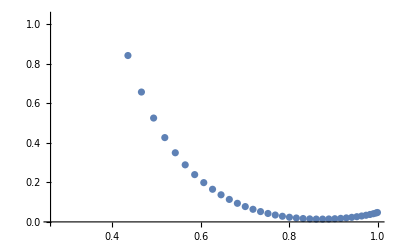

```mathematica
ListPlot[L1]
```

```mathematica
(*SAME exact {l1,l2,l3} as above but in a different order, so τ will be different (related by modular transformation). 
Note that tr(CA^{-1}) is still the same but tr(CA^{-1})/|\hat{f}(0)|^2 is not*)
L2=Table[
Print[k];
findTrCA[setL,setL/2-2k,k,AMat,CMat]
,{k,1,77,2}]
```

1

0.10186356886557+0. ⅈ

{1.-1.73472×10^-18 ⅈ,0.474144+3.38345 ⅈ,-0.474144+3.38345 ⅈ}

3

0.08557485569812+0. ⅈ

{1.+6.93889×10^-18 ⅈ,0.501515+2.72603 ⅈ,-0.501515+2.72603 ⅈ}

5

0.07545780579988+0. ⅈ

{1.+0. ⅈ,0.499669+2.39884 ⅈ,-0.499669+2.39884 ⅈ}

7

0.06741244951662+0. ⅈ

{1.+0. ⅈ,0.500116+2.18517 ⅈ,-0.500116+2.18517 ⅈ}

9

0.06051690181521+0. ⅈ

{1.+0. ⅈ,0.499948+2.02452 ⅈ,-0.499948+2.02452 ⅈ}

11

0.05439788645377+0. ⅈ

{1.+0. ⅈ,0.500027+1.89631 ⅈ,-0.500027+1.89631 ⅈ}

13

0.04886568687005+0. ⅈ

{1.+2.77556×10^-17 ⅈ,0.499984+1.78917 ⅈ,-0.499984+1.78917 ⅈ}

15

0.04381100575745+0. ⅈ

{1.+0. ⅈ,0.50001+1.69724 ⅈ,-0.50001+1.69724 ⅈ}

17

0.03916566152921+0. ⅈ

{1.+0. ⅈ,0.499994+1.61653 ⅈ,-0.499994+1.61653 ⅈ}

19

0.03488471175527+0. ⅈ

{1.+0. ⅈ,0.500005+1.54459 ⅈ,-0.500005+1.54459 ⅈ}

21

0.03093728946557+0. ⅈ

{1.+0. ⅈ,0.499997+1.47958 ⅈ,-0.499997+1.47958 ⅈ}

23

0.0273014776544+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.500002+1.42026 ⅈ,-0.500002+1.42026 ⅈ}

25

0.02396124390897+0. ⅈ

{1.+0. ⅈ,0.499998+1.3656 ⅈ,-0.499998+1.3656 ⅈ}

27

0.02090450652791+0. ⅈ

{1.+0. ⅈ,0.500001+1.3149 ⅈ,-0.500001+1.3149 ⅈ}

29

0.01812185964157+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.499999+1.26754 ⅈ,-0.499999+1.26754 ⅈ}

31

0.0156057009055+0. ⅈ

{1.+0. ⅈ,0.500001+1.22306 ⅈ,-0.500001+1.22306 ⅈ}

33

0.01334961497881+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.499999+1.18108 ⅈ,-0.499999+1.18108 ⅈ}

35

0.01134792486426+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.500001+1.14127 ⅈ,-0.500001+1.14127 ⅈ}

37

0.009595356298635+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+1.10337 ⅈ,-0.5+1.10337 ⅈ}

39

0.008086779730948+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+1.06715 ⅈ,-0.5+1.06715 ⅈ}

41

0.006817006072345+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+1.03241 ⅈ,-0.5+1.03241 ⅈ}

43

0.005780619543519+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.998989 ⅈ,-0.5+0.998989 ⅈ}

45

0.00497183532719+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.966733 ⅈ,-0.5+0.966733 ⅈ}

47

0.00438437231946+0. ⅈ

{1.+0. ⅈ,0.5+0.935513 ⅈ,-0.5+0.935513 ⅈ}

49

0.00401133258433+0. ⅈ

{1.+0. ⅈ,0.5+0.905204 ⅈ,-0.5+0.905204 ⅈ}

51

0.00384507938622+0. ⅈ

{1.+0. ⅈ,0.5+0.8757 ⅈ,-0.5+0.8757 ⅈ}

53

0.00387710492509+0. ⅈ

{1.+5.55112×10^-17 ⅈ,0.5+0.846896 ⅈ,-0.5+0.846896 ⅈ}

55

0.00409787692275+0. ⅈ

{1.-5.55112×10^-17 ⅈ,0.5+0.818698 ⅈ,-0.5+0.818698 ⅈ}

57

0.00449664949881+0. ⅈ

{1.+0. ⅈ,0.5+0.79101 ⅈ,-0.5+0.79101 ⅈ}

59

0.00506121730757+0. ⅈ

{1.+0. ⅈ,0.5+0.763741 ⅈ,-0.5+0.763741 ⅈ}

61

0.00577758068989+0. ⅈ

{1.+0. ⅈ,0.5+0.736793 ⅈ,-0.5+0.736793 ⅈ}

63

0.006629469628292+0. ⅈ

{1.+0. ⅈ,0.500001+0.710066 ⅈ,-0.500001+0.710066 ⅈ}

65

0.007597637139246+0. ⅈ

{1.+0. ⅈ,0.500001+0.683444 ⅈ,-0.500001+0.683444 ⅈ}

67

0.008658759256466+0. ⅈ

{1.-2.77556×10^-17 ⅈ,0.500002+0.656793 ⅈ,-0.500002+0.656793 ⅈ}

69

0.009783621494596+0. ⅈ

{1.-2.77556×10^-17 ⅈ,0.500003+0.629939 ⅈ,-0.500003+0.629939 ⅈ}

71

0.01093389870569+0. ⅈ

{1.+0. ⅈ,0.500006+0.602645 ⅈ,-0.500006+0.602645 ⅈ}

73

0.01205582323729+0. ⅈ

{1.+1.38778×10^-17 ⅈ,0.500016+0.574532 ⅈ,-0.500016+0.574532 ⅈ}

75

0.0130658137977+0. ⅈ

{1.+0. ⅈ,0.500072+0.544898 ⅈ,-0.500072+0.544898 ⅈ}

77

0.01382147930283+0. ⅈ

{1.+0. ⅈ,0.501896+0.5132 ⅈ,-0.501896+0.5132 ⅈ}

{{3.38345,0.251364},{2.72603,0.211415},{2.39884,0.186857},{2.18517,0.167522},{2.02452,0.151093},{1.89631,0.136615},{1.78917,0.12359},{1.69724,0.111723},{1.61653,0.100824},{1.54459,0.0907647},{1.47958,0.0814541},{1.42026,0.0728277},{1.3656,0.0648388},{1.3149,0.0574542},{1.26754,0.0506509},{1.22306,0.0444144},{1.18108,0.038737},{1.14127,0.033617},{1.10337,0.029058},{1.06715,0.0250686},{1.03241,0.0216617},{0.998989,0.018855},{0.966733,0.0166703},{0.935513,0.0151337},{0.905204,0.0142753},{0.8757,0.0141296},{0.846896,0.0147349},{0.818698,0.0161332},{0.79101,0.0183699},{0.763741,0.0214929},{0.736793,0.0255508},{0.710066,0.0305912},{0.683444,0.0366564},{0.656793,0.0437766},{0.629939,0.0519589},{0.602645,0.0611658},{0.574532,0.0712756},{0.544898,0.0819916},{0.5132,0.0921877}}

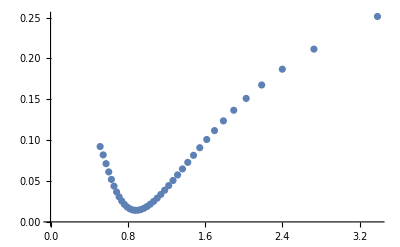

```mathematica
ListPlot[L2]
```

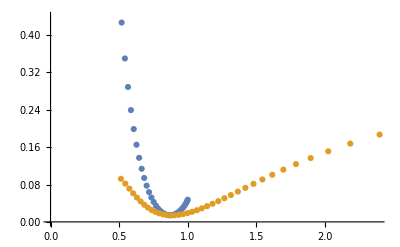

```mathematica
ListPlot[{L1,L2}] (*Don't match at equal τ2 values*)
```

Running test to see how well the values of tr(\wt{C} \wt{A}^{-1})/|\hat{f}(0)|^2 converge as L is increased

```mathematica
L3=Table[
Print[k];
findTrCA[18*k,k,k]
,{k,1,31,2}]
```

1

0.04466939008407+0. ⅈ

{1.+0. ⅈ,0.83216+0.554535 ⅈ,-0.177064+0.585012 ⅈ}

3

0.04004148837671+0. ⅈ

{1.+0. ⅈ,0.822906+0.568178 ⅈ,-0.176555+0.566449 ⅈ}

5

0.0392980798928+0. ⅈ

{1.-1.38778×10^-17 ⅈ,0.823735+0.566975 ⅈ,-0.176383+0.567354 ⅈ}

7

0.03901935352378+0. ⅈ

{1.+0. ⅈ,0.823628+0.56713 ⅈ,-0.176331+0.566998 ⅈ}

9

0.03887848127152+0. ⅈ

{1.-1.38778×10^-17 ⅈ,0.823702+0.567022 ⅈ,-0.176316+0.567081 ⅈ}

11

0.03879517489056+0. ⅈ

{1.+0. ⅈ,0.823685+0.567048 ⅈ,-0.176305+0.567017 ⅈ}

13

0.03874085770088+0. ⅈ

{1.+0. ⅈ,0.823704+0.56702 ⅈ,-0.176301+0.567038 ⅈ}

15

0.038702995639+0. ⅈ

{1.+0. ⅈ,0.823699+0.567028 ⅈ,-0.176298+0.567017 ⅈ}

17

0.0386752882392+0. ⅈ

{1.+0. ⅈ,0.823706+0.567017 ⅈ,-0.176296+0.567024 ⅈ}

19

0.03865424704268+0. ⅈ

{1.-6.93889×10^-18 ⅈ,0.823704+0.56702 ⅈ,-0.176295+0.567015 ⅈ}

21

0.0386377955598+0. ⅈ

{1.+0. ⅈ,0.823707+0.567015 ⅈ,-0.176294+0.567019 ⅈ}

23

0.03862462612352+0. ⅈ

{1.-6.93889×10^-18 ⅈ,0.823706+0.567017 ⅈ,-0.176293+0.567014 ⅈ}

25

0.03861387718433+0. ⅈ

{1.+6.93889×10^-18 ⅈ,0.823708+0.567014 ⅈ,-0.176293+0.567016 ⅈ}

27

0.03860495969322+0. ⅈ

{1.-6.93889×10^-18 ⅈ,0.823708+0.567015 ⅈ,-0.176292+0.567013 ⅈ}

29

0.03859745825274+0. ⅈ

{1.+6.93889×10^-18 ⅈ,0.823709+0.567013 ⅈ,-0.176292+0.567015 ⅈ}

31

0.03859107213171+0. ⅈ

{1.+0. ⅈ,0.823708+0.567014 ⅈ,-0.176291+0.567013 ⅈ}

{{0.554535,0.304482},{0.568178,0.292663},{0.566975,0.28675},{0.56713,0.285139},{0.567022,0.284073},{0.567048,0.283544},{0.56702,0.283139},{0.567028,0.282889},{0.567017,0.282684},{0.56702,0.282542},{0.567015,0.282421},{0.567017,0.282331},{0.567014,0.282252},{0.567015,0.282191},{0.567013,0.282136},{0.567014,0.282091}}

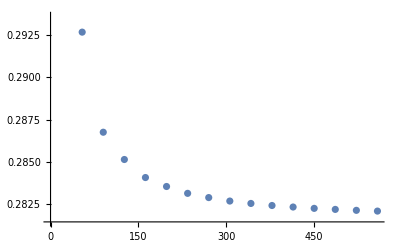

```mathematica
ListPlot[Table[{18*k,L3[[(k-1)/2+1,2]]},{k,1,31,2}]]
```

### Stress tensor 1-pt function

Equivalent of the C matrix but for X_m X_n instead of X_1 X_-1

```mathematica
(****CHECK THE SIGN in the exponent*)
```

```mathematica
DirectCMat[L_,m_,n_]:=DirectFMat[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&]
DirectCMatN[L_,m_,n_,NPrec_]:=DirectFMatN[L,(((Abs[m]!)(Abs[n]!))/#1^2 Exp[-I*2*Pi*(m*#2+n*#3)/#1])&,NPrec]
```

```mathematica
DirectTracedCMat[L_,m_,n_,l1_,l2_]:=
DirectTracedMat[L,l1,l2,DirectCMat[L,m,n]]
```

```mathematica
DirectTracedCMatN[L_,m_,n_,l1_,l2_,NPrec_]:=
DirectTracedMat[L,l1,l2,DirectCMatN[L,m,n,NPrec]]
```